```mathematica
SetDirectory["/Users/cdschillaci/Desktop/Efimov in a Well/BH C++ Code/data"];
```

```mathematica
eMin=2.5; eMax=7.5;
a2InvMin=0;a2InvMax=0;
a3Min=-.25;a3Max=.25;

aScale[x_]:=Sign[x]x^2;
eScale[x_]:=x;
```

```mathematica
rawData=Import[StringJoin["PairsBya2Inv.csv"]];
rawData=Sort[rawData,If[#1[[1]]==#2[[1]],#1[[2]]<#2[[2]],#1[[1]]<#2[[1]]]&];
```

```mathematica
ee={};

result={};

Off[Part::partw];
For[rawIndex=1,rawIndex≤Length[rawData],rawIndex++,

AppendTo[ee,{rawData[[rawIndex,3]],rawData[[rawIndex,4]]}];

(* When all e for a given (a2Inv, a3) have been loaded, do some work *)
(* Also does work when it arrives at the end of the list rawData *)
If[rawData[[rawIndex,1]]!=rawData[[rawIndex+1,1]]||rawData[[rawIndex,2]]!=rawData[[rawIndex+1,2]]||rawIndex==Length[rawData],

(* interpolate the {energy,eigenvalue} data *)
f=Interpolation[ee];

(* find the set of eigenvalues within 0.003 of 1 as a set of guesses for the root solver *)
eclose={};
Do[
If[Abs[ee[[i,2]]-1.0]<.004,AppendTo[eclose,ee[[i,1]]]],
{i,1,Length[ee]}
];

(* use the values saved in eclose and the interpolated data to find the energies at which an eigenvalue of mm=1. Save these to "es" *)
es={};
AppendTo[es,FindRoot[f[x]-1==0,{x,eclose[[1]]}][[1,2]]];
Do[
answer=FindRoot[f[x]-1==0,{ x,eclose[[i]] }][[1,2]];
If[Abs[answer-es[[Dimensions[es][[1]]]]]>.001,AppendTo[es,answer]],
{i,2,Dimensions[eclose][[1]]}
];

(* now append the interpolated energy eigenvalues as pairs { ascale[1/a2], a3, energy} to the table "result" *)
Do[
AppendTo[result,{aScale[rawData[[rawIndex,1]]],rawData[[rawIndex,2]],eScale[es[[i]]]}],
{i,1,Dimensions[es][[1]]}
];

(* reset "ee" *)
ee={};
];
];
result=Union[N[result,6]];
```

```mathematica
(* Gives a table of  ( 1/a2Inv^2 , a3 , e ) 's  *)
result
```

{{0,-0.1,2.849},{0,-0.1,4.74078},{0,-0.1,4.99994},{0,-0.1,6.62762},{0,-0.1,6.86947},{0,-0.1,7.00343},{0,-0.05,2.93602},{0,-0.05,4.8997},{0,-0.05,4.99877},{0,-0.05,6.85621},{0,-0.05,6.95206},{0,-0.05,7.0072},{0,0,3.98878},{0,0,6.14174},{0,0,7.46528},{0,0.05,3.04635},{0,0.05,4.99902},{0,0.05,5.06416},{0,0.05,7.0393},{0,0.05,7.08831},{0,0.1,3.07968},{0,0.1,4.99911},{0,0.1,5.11272},{0,0.1,7.02456},{0,0.1,7.05503},{0,0.1,7.14775}}

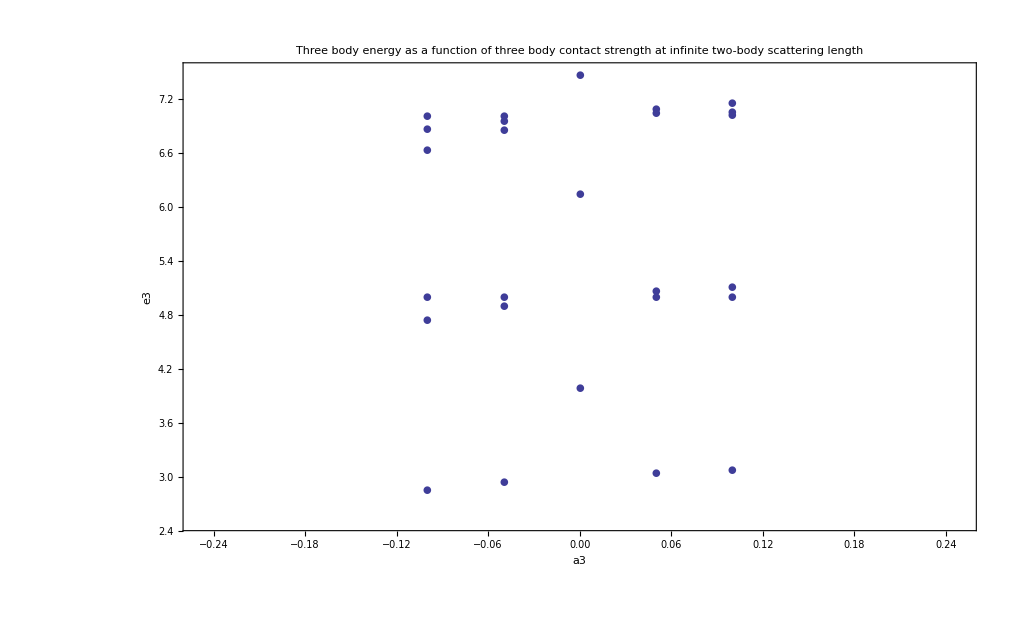

```mathematica
temp=Table[{result[[i,2]],result[[i,3]]},{i,1,Length[result]}];
(*temp2={{0,1.624139},{0,3.905},{0,5.467},{0,6.16},{0,7.819},{0,7.457},{0,8.166}};*)
temp2={{}};
ListPlot[{temp,temp2},PlotMarkers->{Automatic, 10},PlotRange->{{a3Min,a3Max},{eMin,eMax}},Frame->True,FrameLabel->{a3,e3},PlotLabel->"Three body energy as a function of three body contact strength at infinite two-body scattering length"]
```

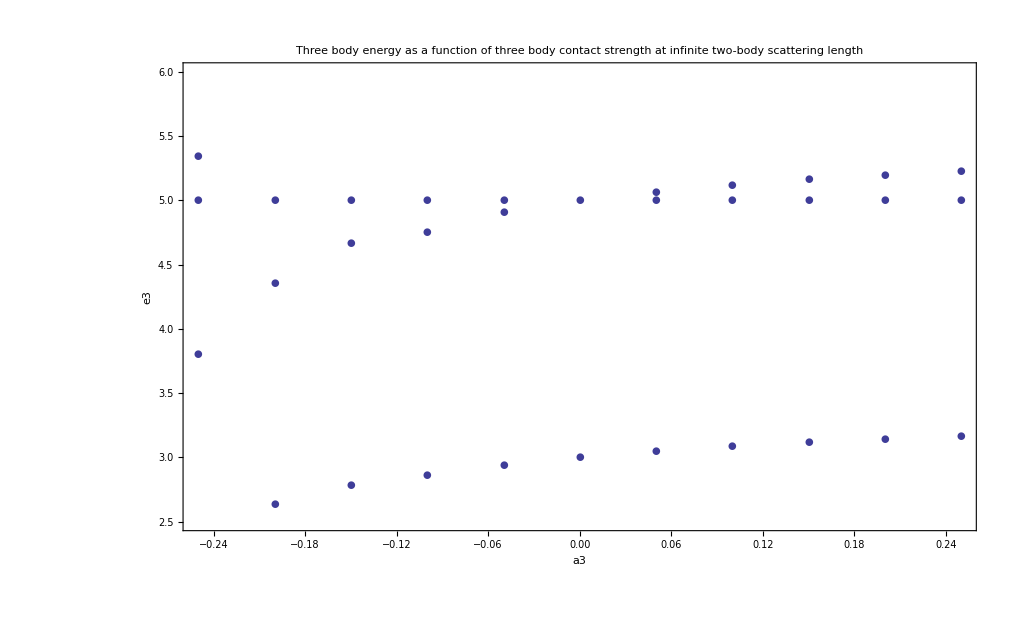

-Graphics-